## Chapter 12 [Partial Differential Equations (PDEs)]

## 12.1 Wave Equation, Separation Of Variables, Animation

```mathematica
Clear["Global`*"]
```

```mathematica
U[x,t]=F[x]G[t]
```

F[x] G[t]

```mathematica
pde=D[U[x,t],t,t]==c^2D[U[x,t],x,x]
```

F[x] G''[t]==c^2 G[t] F''[x]

```mathematica
eq=pde[[1]]/(c^2U[x,t])==pde[[2]]/(c^2U[x,t])
```

G''[t]/(c^2 G[t])==F''[x]/F[x]

```mathematica
sol1=DSolve[eq[[2]]==-p^2,F[x],x]
```

{{F[x]→C[1] Cos[p x]+C[2] Sin[p x]}}

```mathematica
s2=(sol1[[1,1,2]]/.x->0)==0
```

C[1]==0

```mathematica
s3=sol1/.{C[1]->0,C[2]->1}
```

{{F[x]→Sin[p x]}}

```mathematica
s4=s3/.x->L
```

{{F[L]→Sin[L p]}}

```mathematica
p=n Pi/L
```

(n π)/L

```mathematica
solF=s3
```

{{F[x]→Sin[(n π x)/L]}}

```mathematica
solG=DSolve[eq[[1]]==-p^2,G[t],t]
```

{{G[t]→C[1] Cos[(c n π t)/L]+C[2] Sin[(c n π t)/L]}}

```mathematica
U[x,t]=solF[[1,1,2]]solG[[1,1,2]]
```

(C[1] Cos[(c n π t)/L]+C[2] Sin[(c n π t)/L]) Sin[(n π x)/L]

```mathematica
Animate[Plot[Sin[t]Sin[x],{x,0,Pi},PlotRange->{-1,1}],{t,0,2Pi}]
```

## 12.2 One-Dimensional Heat Equation

```mathematica
Bn=2/Pi(Integrate[x Sin[n x],{x,0,Pi/2}]+Integrate[(Pi-x)Sin[n x],{x,Pi/2,Pi}])
```

1/π 2 ((-1/2 n π Cos[(n π)/2]+Sin[(n π)/2])/n^2+(n π Cos[(n π)/2]+2 Sin[(n π)/2]-2 Sin[n π])/(2 n^2))

```mathematica
S=Sum[Bn Sin[n x]Exp[-n^2 t],{n,1,13}]
```

(4 ⅇ^-t Sin[x])/π-(4 ⅇ^(-9 t) Sin[3 x])/(9 π)+(4 ⅇ^(-25 t) Sin[5 x])/(25 π)-(4 ⅇ^(-49 t) Sin[7 x])/(49 π)+(4 ⅇ^(-81 t) Sin[9 x])/(81 π)-(4 ⅇ^(-121 t) Sin[11 x])/(121 π)+(4 ⅇ^(-169 t) Sin[13 x])/(169 π)

```mathematica
S0=N[S/.t->0]
```

1.27324 Sin[x]-0.141471 Sin[3. x]+0.0509296 Sin[5. x]-0.0259845 Sin[7. x]+0.015719 Sin[9. x]-0.0105226 Sin[11. x]+0.00753396 Sin[13. x]

```mathematica
S1=S/.t->0.1;
```

```mathematica
S2=S/.t->0.2;
```

```mathematica
S10=S/.t->1;
```

```mathematica
S20=S/.t->2;
```

```mathematica
S30=S/.t->3;
```

```mathematica
P1=Plot[{S0,S1,S2,S10,S20,S30},{x,0,Pi}];
```

```mathematica
P2=Plot[t,{t,0,Pi/2}];
```

```mathematica
P3=Plot[Pi-t,{t,Pi/2,Pi}];
```

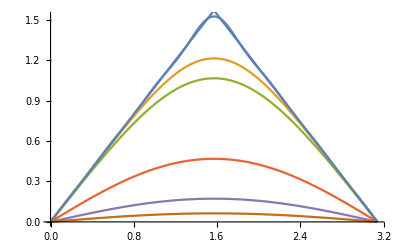

```mathematica
Show[P1,P2,P3]
```

## 12.3 Two Dimensional Heat Equation, Laplace Equation

```mathematica
Bn=2/(Pi Sinh[n Pi/2])Integrate[1 Sin[n x],{x,0,Pi}]
```

(2 (1-Cos[n π]) Csch[(n π)/2])/(n π)

```mathematica
u30=Sum[Bn Sin[n x]Sinh[n y],{n,1,30}]
```

(4 Csch[π/2] Sin[x] Sinh[y])/π+(4 Csch[(3 π)/2] Sin[3 x] Sinh[3 y])/(3 π)+(4 Csch[(5 π)/2] Sin[5 x] Sinh[5 y])/(5 π)+(4 Csch[(7 π)/2] Sin[7 x] Sinh[7 y])/(7 π)+(4 Csch[(9 π)/2] Sin[9 x] Sinh[9 y])/(9 π)+(4 Csch[(11 π)/2] Sin[11 x] Sinh[11 y])/(11 π)+(4 Csch[(13 π)/2] Sin[13 x] Sinh[13 y])/(13 π)+(4 Csch[(15 π)/2] Sin[15 x] Sinh[15 y])/(15 π)+(4 Csch[(17 π)/2] Sin[17 x] Sinh[17 y])/(17 π)+(4 Csch[(19 π)/2] Sin[19 x] Sinh[19 y])/(19 π)+(4 Csch[(21 π)/2] Sin[21 x] Sinh[21 y])/(21 π)+(4 Csch[(23 π)/2] Sin[23 x] Sinh[23 y])/(23 π)+(4 Csch[(25 π)/2] Sin[25 x] Sinh[25 y])/(25 π)+(4 Csch[(27 π)/2] Sin[27 x] Sinh[27 y])/(27 π)+(4 Csch[(29 π)/2] Sin[29 x] Sinh[29 y])/(29 π)

```mathematica
Plot3D[u30,{x,0,Pi},{y,0,Pi/2},ViewPoint->{1,2,1.5}]
```

-Graphics3D-

```mathematica
W=u30/.y->Pi/2;
```

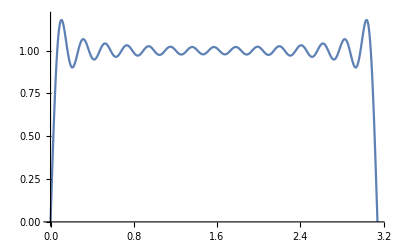

```mathematica
Plot[W,{x,0,Pi},PlotRange->{0,1.2}]
```

## 12.4 Rectangular Membrane, Double Fourier Series

```mathematica
f=1/10(4x-x^2)(2y-y^2)
```

1/10 (4 x-x^2) (2 y-y^2)

```mathematica
Plot3D[f,{x,0,4},{y,0,2}]
```

-Graphics3D-

```mathematica
Clear[m,n]
```

```mathematica
a=4;b=2;
```

```mathematica
Bmn=4/(a b)Integrate[Integrate[f Sin[m Pi x/a]Sin[n Pi y/b],{x,0,a}],{y,0,b}]
```

1/(5 m^3 n^3 π^6)128 (-2+2 Cos[m π]+m π Sin[m π]) (-2+2 Cos[n π]+n π Sin[n π])

```mathematica
Lmn=5Pi Sqrt[m^2/a^2+n^2/b^2]
```

5 √(m^2/16+n^2/4) π

```mathematica
umn=Bmn Cos[Lmn t]Sin[m Pi x/a]Sin[n Pi y/b]
```

1/(5 m^3 n^3 π^6)128 Cos[5 √(m^2/16+n^2/4) π t] (-2+2 Cos[m π]+m π Sin[m π]) (-2+2 Cos[n π]+n π Sin[n π]) Sin[(m π x)/4] Sin[(n π y)/2]

```mathematica
S=umn/.{m->1,n->1}
```

(2048 Cos[5/4 √5 π t] Sin[(π x)/4] Sin[(π y)/2])/(5 π^6)

```mathematica
S0=S/.t->0
```

(2048 Sin[(π x)/4] Sin[(π y)/2])/(5 π^6)

```mathematica
Plot3D[S0,{x,0,4},{y,0,2}]
```

-Graphics3D-

## 12.5 Laplacian. Circular Membrane, Bessel Equation

```mathematica
SetCoordinates[Polar[r,theta]]
```

Coordinates::invalid: Polar[r,theta] is not a valid coordinate system specification.

SetCoordinates[Polar[r,theta]]

```mathematica
Clear[r,z]
```

```mathematica
SetCoordinates[Cylindrical[r,theta,z]]
```

Cylindrical[r,theta,z]

```mathematica
Clear[W]
```

```mathematica
u[r,t]=W[r]G[t]
```

G[t] W[r]

```mathematica
lap=Laplacian[u[r,t]]
```

(G[t] W'[r]+r G[t] W''[r])/r

```mathematica
pde=D[u[r,t],t,t]==c^2lap
```

W[r] G''[t]==(c^2 (G[t] W'[r]+r G[t] W''[r]))/r

```mathematica
pde[[1]]
```

W[r] G''[t]

```mathematica
eq1=pde[[1]]/(c^2u[r,t])==Simplify[pde[[2]]/(c^2u[r,t])]
```

G''[t]/(c^2 G[t])==(W'[r]+r W''[r])/(r W[r])

```mathematica
eq2=eq1[[2]]+k^2==0
```

k^2+(W'[r]+r W''[r])/(r W[r])==0

```mathematica
eq3=Together[eq2[[1]]W[r]]==0
```

(k^2 r W[r]+W'[r]+r W''[r])/r==0

```mathematica
Simplify[%]
```

k^2 W[r]+W'[r]/r+W''[r]==0

```mathematica
DSolve[eq3,W[r],r]
```

{{W[r]→BesselJ[0,k r] C[1]+BesselY[0,k r] C[2]}}

```mathematica
solJ=%/.{C[1]->1,C[2]->0}
```

{{W[r]→BesselJ[0,k r]}}

```mathematica
solJ[[1,1,2]]
```

BesselJ[0,k r]

```mathematica
zero1=FindRoot[BesselJ[0,s]==0,{s,2}]
```

{s→2.40483}

```mathematica
zero2=FindRoot[BesselJ[0,s]==0,{s,6}]
```

{s→5.52008}

```mathematica
zero3=FindRoot[BesselJ[0,s]==0,{s,10}]
```

{s→8.65373}

```mathematica
zero1[[1,2]]
```

2.40483

```mathematica
ParametricPlot3D[{r Cos[theta],r Sin[theta],BesselJ[0,zero1[[1,2]]r]},{r,0,1},{theta,0,2Pi}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{r Cos[theta],r Sin[theta],BesselJ[0,zero2[[1,2]]r]},{r,0,1},{theta,0,2Pi}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{r Cos[theta],r Sin[theta],BesselJ[0,zero3[[1,2]]r]},{r,0,1},{theta,0,2Pi}]
```

-Graphics3D-

## -------------------The End------------------